## PTA analysis

```mathematica
ResponseFunction[theta_,phi_,pa_]:=Module[{waveVector,UnitM,UnitN,EPlus,ECross,responsePlus,responseCross,cosPhi,sinPhi,cosTheta,sinTheta},(*Precompute trigonometric functions for efficiency*)
cosPhi=Cos[phi];
sinPhi=Sin[phi];
cosTheta=Cos[theta];
sinTheta=Sin[theta];

(*Define vectors*)
waveVector={sinTheta cosPhi,sinTheta sinPhi,cosTheta};
UnitN={-sinPhi,cosPhi,0};
UnitM={cosTheta cosPhi,cosTheta sinPhi,-sinTheta};

(*Polarization tensors using TensorProduct for outer product*)
EPlus=TensorProduct[UnitM,UnitM]-TensorProduct[UnitN,UnitN];
ECross=TensorProduct[UnitM,UnitN]+TensorProduct[UnitN,UnitM];

(*Response functions using Dot for dot product*)
responsePlus=1/2 Sum[pa[[i]] pa[[j]] EPlus[[i,j]]/(1+waveVector.pa),{i,Length[pa]},{j,Length[pa]}];
responseCross=1/2 Sum[pa[[i]] pa[[j]] ECross[[i,j]]/(1+waveVector.pa),{i,Length[pa]},{j,Length[pa]}];

(*Return all results in a structured list*)
<|"WaveVector"->waveVector,"UnitM"->UnitM,"UnitN"->UnitN,"EPlus"->EPlus,"ECross"->ECross,"ResponsePlus"->responsePlus,"ResponseCross"->responseCross|>]
```

```mathematica
FromVectorToAngles[waveVector_]:=Module[{theta,phi,cosTheta,sinTheta,cosPhi,sinPhi,th,ph},

cosTheta=waveVector[[3]];
sinTheta=Sqrt[1-cosTheta^2];
(*Check for division by zero (when sinTheta is zero)*)

If[sinTheta==0,(*Special case when sinTheta is zero,waveVector points along z-axis*)
ph=0;(*or any other value,phi is arbitrary in this case*)
th=If[cosTheta>0,0,Pi]; (*theta is 0 if pointing up,Pi if down*),

(*General case*)

cosPhi=waveVector[[1]]/sinTheta;
sinPhi=waveVector[[2]]/sinTheta;

th=ArcCos[cosTheta];
ph=ArcTan[waveVector[[2]],waveVector[[1]]]; (*Use ArcTan for full range*)];
<|"Phi"->ph,"Theta"->th|>]

(*Define the PlotYlm function*)
PlotYlm[dataYlm_,dataXi_]:=Module[{numXi,lMax,plots,xiValues},
(*Extract the number of xi values and range of l and m*)
numXi=Length[dataXi];
lMax=Length[dataYlm[[1]]]-1;
xiValues=dataXi;
(*Generate the plots for each combination of l and m*)
plots=Table[Module[{data},
(*Extract data points for a specific l and m*)
data=Table[{xiValues[[i]],dataYlm[[i,l+1,m+l+1]]},{i,1,numXi}];
(*Create the plot*)
ListPlot[data,PlotRange->All,(*AxesLabel->{"\!\(\*SubscriptBox[\(ξ\), \(i\)]\)","\!\(\*SuperscriptBox[\(Γ\), \(V\)]\)[l,m]"},*)PlotLabel->Style[StringForm["Plot for l = ``, m = ``",l,m],FontSize->14],PlotStyle->{Thick,RandomColor[]},Mesh->All,MeshStyle->PointSize[Small],Joined->True]],{l,0,lMax},{m,-l,l}];
(*Display all plots*)
plots];

(*Define common trigonometric functions outside the loop for efficiency*)
TrigonometricCache[theta_,phi_]:=Module[{sTheta,cTheta,sPhi,cPhi},sTheta=Sin[theta];cTheta=Cos[theta];
sPhi=Sin[phi];cPhi=Cos[phi];
{sTheta,cTheta,sPhi,cPhi}];

(*Simplify PulsarGeometryTerms function by removing redundant computations*)
PulsarGeometryTerms[xvec_,theta_,phi_,trigCache_]:=Module[{omegaHat,mHat,nHat,ePlus,eCross,FPlus,FCross,denom,DPlus,DCross,factor,Pulsar},
(*Retrieve precomputed trigonometric values*)
{sTheta,cTheta,sPhi,cPhi}=trigCache;

(*Define the vectors*)
omegaHat={sTheta cPhi,sTheta sPhi,cTheta};
mHat={sPhi,-cPhi,0};
nHat={cTheta cPhi,cTheta sPhi,-sTheta};

(*Define the tensors,without simplifying unnecessarily*)
ePlus=Outer[Times,mHat,mHat]-Outer[Times,nHat,nHat];
eCross=Outer[Times,mHat,nHat]+Outer[Times,nHat,mHat];

(*Calculate F+and F×*)
Pulsar=1/2 TensorProduct[xvec,xvec];
FPlus=ePlus.Pulsar;
FCross=eCross.Pulsar;

(*Define the denominator*)
denom=1+omegaHat.xvec+10^(-10);

(*To avoid division by zero*)(*Calculate D+and D×*)
DPlus=Tr[FPlus/denom];
DCross=Tr[FCross/denom];

(*Define the factor term*)
factor=DPlus^2+DCross^2;

(*Return the factor for integration*)
{DPlus,DCross,factor}];
```

#### Some random plotting

```mathematica
PacletSiteUpdate["https://pacletserver.bhptoolkit.org"]
```

PacletSiteObject[<|URL→https://pacletserver.bhptoolkit.org,Name→Black Hole Perturbation Toolkit Paclet Server,Local→False,Type→Server|>]

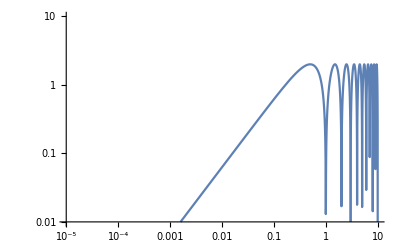

```mathematica
TransferfunctionPTA=Abs[1-Exp[-I 2 Pi α]];
LogLogPlot[TransferfunctionPTA,{α,1/10^5,10},PlotRange->{{10^-5,10},{10^-2,10}}]
```

## Tests:

```mathematica
Needs["SpinWeightedSpheroidalHarmonics`"]
```

```mathematica
Table[SpinWeightedSphericalHarmonicY[2,2,m,θ,ϕ],{l,0,2},{m,-l,l}]
```

{{√(15/(2 π)) Cos[θ/2]^2 Sin[θ/2]^2},{-ⅇ^(-ⅈ ϕ) √(5/π) Cos[θ/2]^3 Sin[θ/2],√(15/(2 π)) Cos[θ/2]^2 Sin[θ/2]^2,-ⅇ^(ⅈ ϕ) √(5/π) Cos[θ/2] Sin[θ/2]^3},{1/2 ⅇ^(-2 ⅈ ϕ) √(5/π) Cos[θ/2]^4,-ⅇ^(-ⅈ ϕ) √(5/π) Cos[θ/2]^3 Sin[θ/2],√(15/(2 π)) Cos[θ/2]^2 Sin[θ/2]^2,-ⅇ^(ⅈ ϕ) √(5/π) Cos[θ/2] Sin[θ/2]^3,1/2 ⅇ^(2 ⅈ ϕ) √(5/π) Sin[θ/2]^4}}

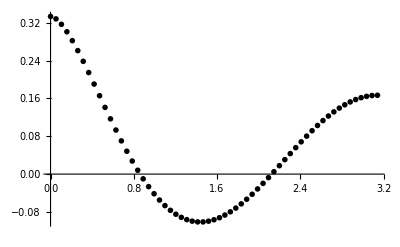

```mathematica
(*Define the pulsar vector*)
xvec={0,0,1};

(*Define the list of Xi values*)
Xi=Table[i/60 Pi,{i,0,60}];

(*Generate the corresponding vectors xve2 for each Xi value*)
xve2=N[{Sin[#],0,Cos[#]}]&/@Xi;

(*Cache trigonometric calculations and optimize the integration process*)
resultIntensity=Table[Module[{trigCache,integrand},

trigCache=TrigonometricCache[theta,phi];
integrand=(PulsarGeometryTerms[xvec,theta,phi,trigCache][[1]] PulsarGeometryTerms[xve2[[i]],theta,phi,trigCache][[1]]+PulsarGeometryTerms[xvec,theta,phi,trigCache][[2]] PulsarGeometryTerms[xve2[[i]],theta,phi,trigCache][[2]]) Sin[theta]/(4 Pi);

Quiet[NIntegrate[integrand,{theta,0,Pi},{phi,0,2 Pi}]]],{i,1,Length[xve2]}];

(*Plot the results*)
ListPlot[Table[{Xi[[i]],resultIntensity[[i]]},{i,1,Length[Xi]}],PlotRange->All,PlotStyle->{Black,PointSize[0.01]}]
```

```mathematica
(*Cache trigonometric calculations and optimize the integration process*)
resultCircularPolariztion=Table[Module[{trigCache,integrand},

trigCache=TrigonometricCache[theta,phi];
integrand=(PulsarGeometryTerms[xvec,theta,phi,trigCache][[1]] PulsarGeometryTerms[xve2[[i]],theta,phi,trigCache][[2]]-PulsarGeometryTerms[xvec,theta,phi,trigCache][[2]] PulsarGeometryTerms[xve2[[i]],theta,phi,trigCache][[1]]) Sin[theta]/(4 Pi);

Quiet[NIntegrate[integrand,{theta,0,Pi},{phi,0,2 Pi}]]],{i,1,Length[xve2]}];
```

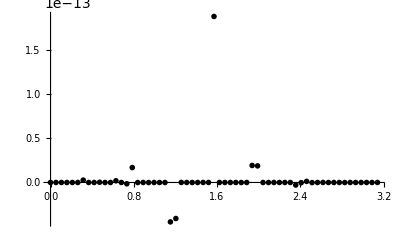

```mathematica
(*Plot the results*)
ListPlot[Table[{Xi[[i]],resultCircularPolariztion[[i]]},{i,1,Length[Xi]}],PlotRange->All,PlotStyle->{Black,PointSize[0.01]}]
```

```mathematica
resultIntensityYlm=Table[Module[{trigCache,integrand},

trigCache=TrigonometricCache[theta,phi];
integrand=SphericalHarmonicY[l,m,theta,phi](PulsarGeometryTerms[xvec,theta,phi,trigCache][[1]] PulsarGeometryTerms[xve2[[i]],theta,phi,trigCache][[1]]+PulsarGeometryTerms[xvec,theta,phi,trigCache][[2]] PulsarGeometryTerms[xve2[[i]],theta,phi,trigCache][[2]]) Sin[theta]/(4 Pi);

Quiet[NIntegrate[integrand,{theta,0,Pi},{phi,0,2 Pi}]]],{i,1,Length[xve2]},{l,0,3},{m,-l,l}];
```

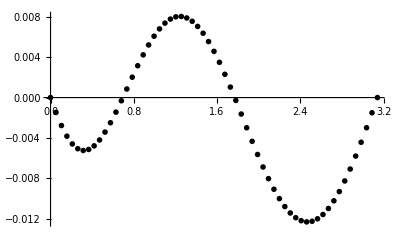

```mathematica
ListPlot[Table[{Xi[[i]],resultIntensityYlm[[i,2,1]]},{i,1,Length[Xi]}],PlotRange->All,PlotStyle->{Black,PointSize[0.01]}]
```

```mathematica
resultCircularPolariztionYlm=Table[Module[{trigCache,integrand},

trigCache=TrigonometricCache[theta,phi];
integrand=-I SphericalHarmonicY[l,m,theta,phi](PulsarGeometryTerms[xvec,theta,phi,trigCache][[1]] PulsarGeometryTerms[xve2[[i]],theta,phi,trigCache][[2]]-PulsarGeometryTerms[xvec,theta,phi,trigCache][[2]] PulsarGeometryTerms[xve2[[i]],theta,phi,trigCache][[1]]) Sin[theta]/(4 Pi);

Quiet[NIntegrate[integrand,{theta,0,Pi},{phi,0,2 Pi}]]],{i,1,Length[xve2]},{l,0,3},{m,-l,l}];
```

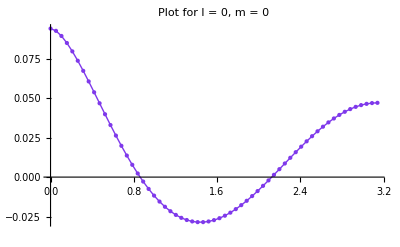
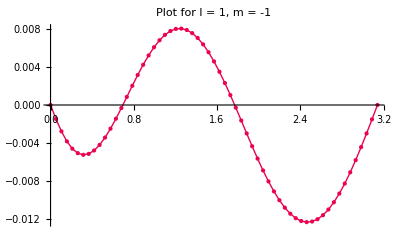
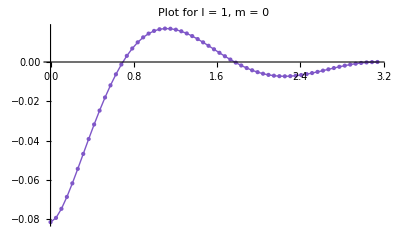
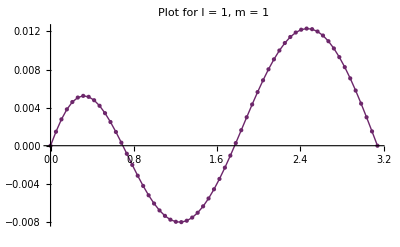
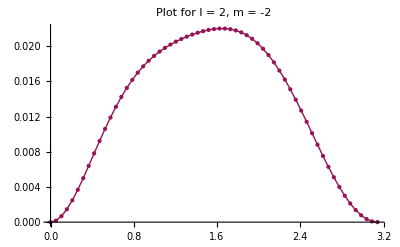
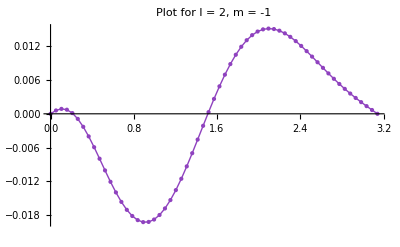
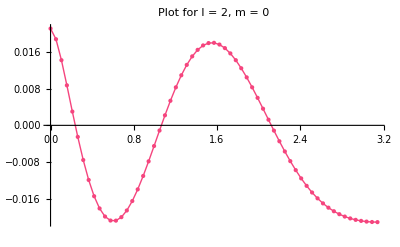
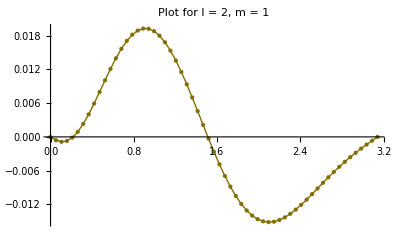

```mathematica
PlotYlm[resultIntensityYlm,Xi]
```

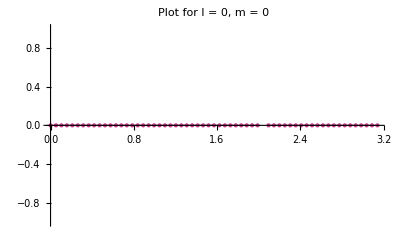
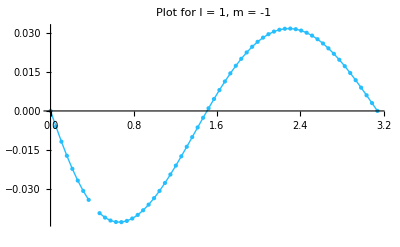
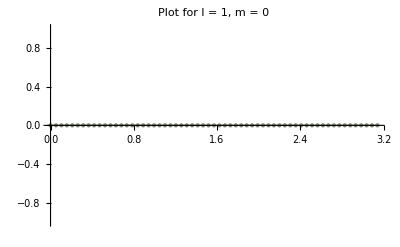
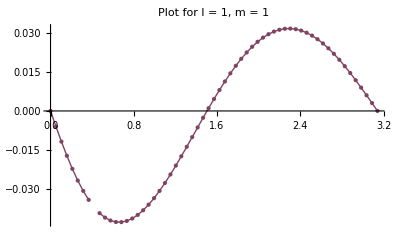
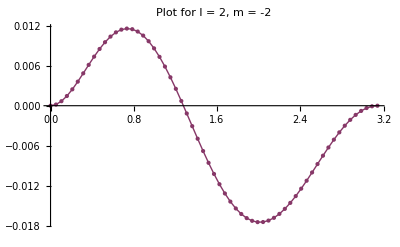
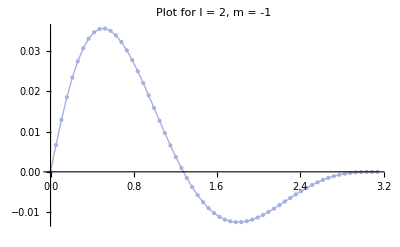
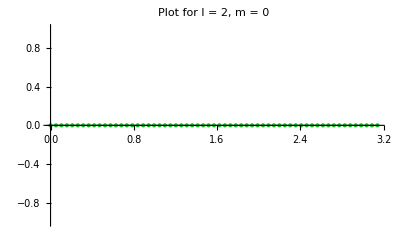
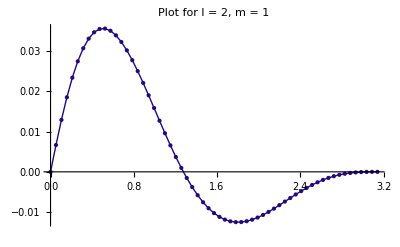

```mathematica
PlotYlm[resultCircularPolariztionYlm,Xi]
```

```mathematica
(*change normalization of ORFs*)
resultIntensityYlm4pi=resultIntensityYlm*Sqrt[4 Pi];
resultCircularPolariztionYlm4pi=resultCircularPolariztionYlm*Sqrt[4 Pi];
```

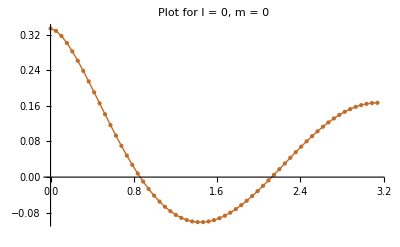
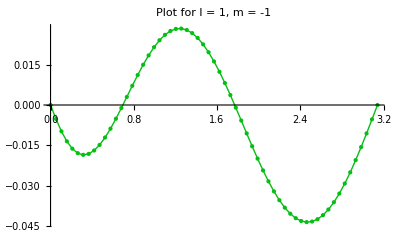
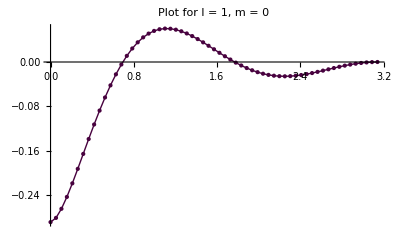
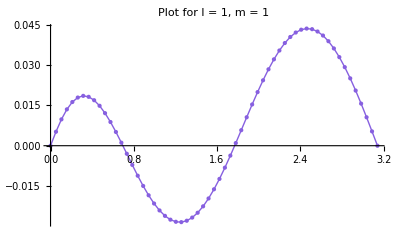
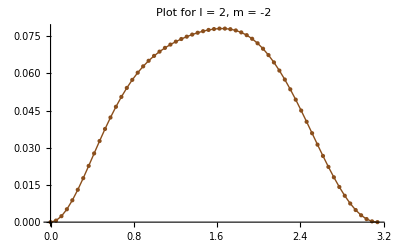
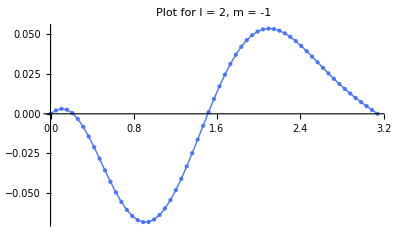
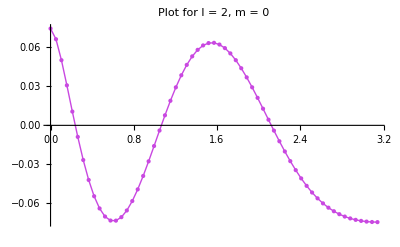
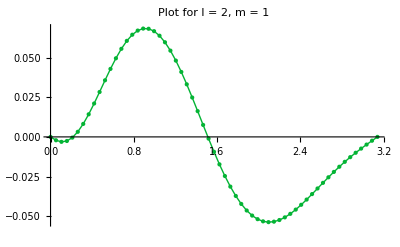

```mathematica
PlotYlm[resultIntensityYlm4pi,Xi]
```

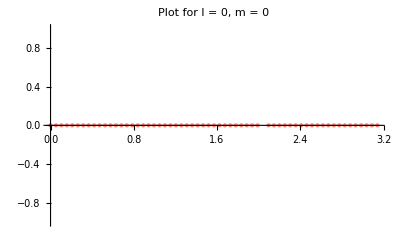
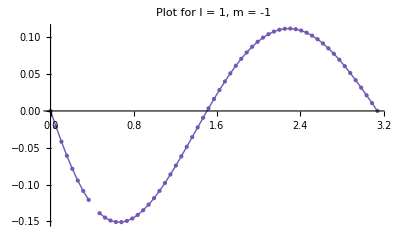
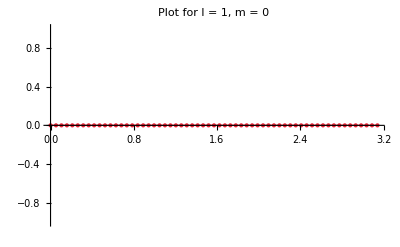
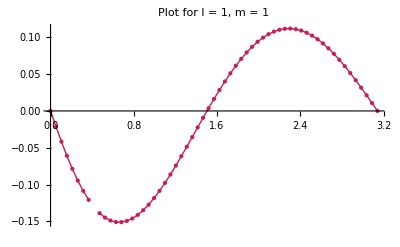
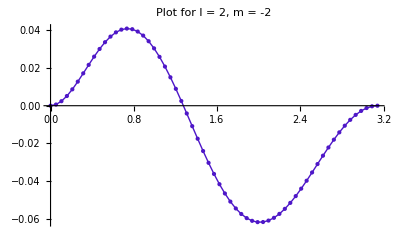
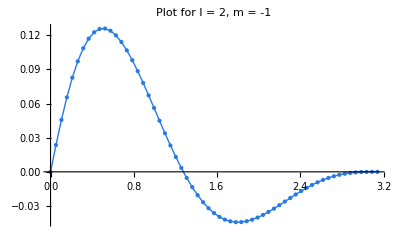
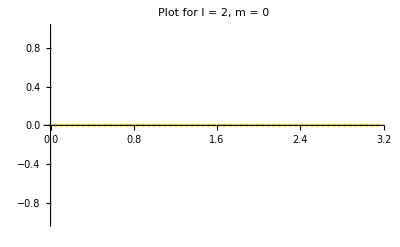
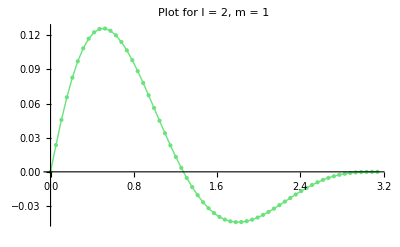

```mathematica
PlotYlm[resultCircularPolariztionYlm4pi,Xi]
```

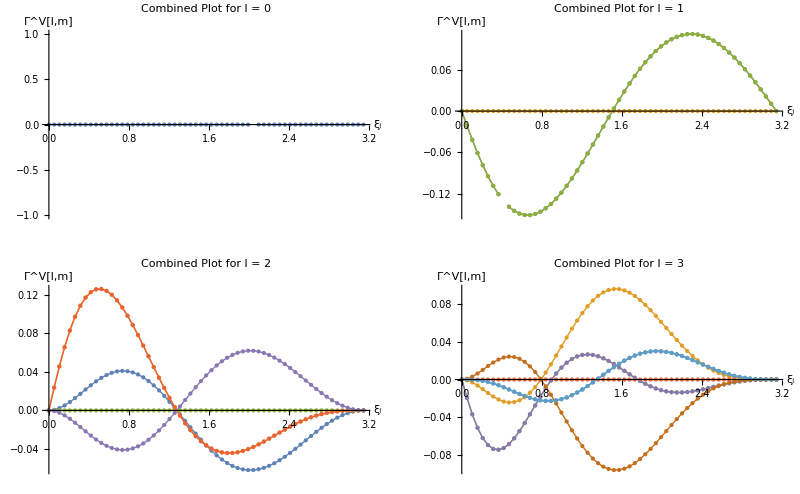

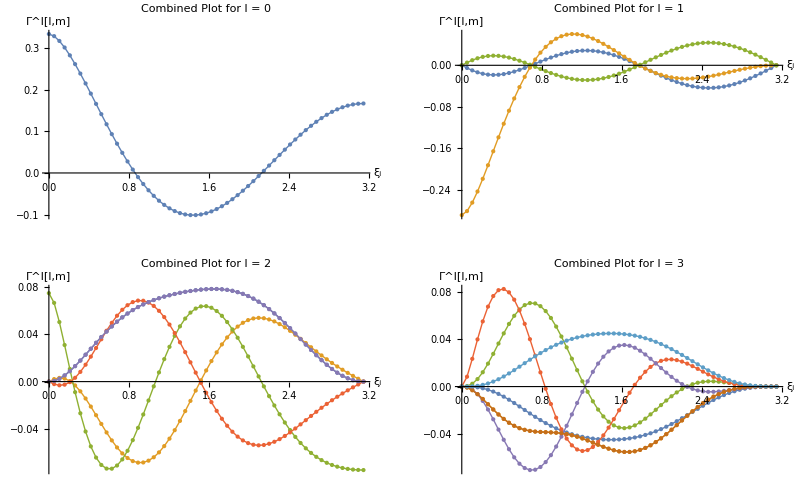

```mathematica
(*Define the PlotYlmCombined function with a name argument and legends*)PlotYlmCombinedWithLegend[dataYlm_,dataXi_,name_]:=Module[{numXi,lMax,combinedPlots,xiValues,colorList},

(*Extract the number of xi values and range of l*)
numXi=Length[dataXi];
lMax=Length[dataYlm[[1]]]-1;
(*Assuming l goes up to lMax*)
xiValues=dataXi;
colorList=ColorData[97,"ColorList"];
(*Using a predefined color list*)
(*Generate the combined plots for each l value*)combinedPlots=Table[Module[{data,mPlots,legendLabels},(*Generate plots for each m value for a specific l*)mPlots=Table[data=Table[{xiValues[[i]],dataYlm[[i,l+1,m+l+1]]},{i,1,numXi}];
ListLinePlot[data,PlotStyle->{Thick,colorList[[m+l+1]]},Mesh->All,MeshStyle->PointSize[Small],Joined->True],{m,-l,l}];
(*Create legend labels for each m*)
legendLabels=Table[Style[StringForm["m = ``",m],colorList[[m+l+1]]],{m,-l,l}];
(*Combine all m plots for the same l into one with legends*)Show[mPlots,PlotRange->All,AxesLabel->{"\!\(\*SubscriptBox[\(ξ\), \(i\)]\)",StringForm["\!\(\*SuperscriptBox[\(Γ\), ``]\)[l,m]",name]},PlotLabel->Style[StringForm["Combined Plot for l = ``",l],FontSize->14],PlotLegends->Placed[LineLegend[legendLabels],{Right,Top}]]],{l,0,lMax}];
(*Display all combined plots*)
GraphicsGrid[Partition[combinedPlots,2]]];

PlotYlmCombinedWithLegend[resultCircularPolariztionYlm4pi,Xi,"V"]
PlotYlmCombinedWithLegend[resultIntensityYlm4pi,Xi,"I"]
```